# Lagrange Points: Developing an Intuition

When two large objects orbit one-another, there exist equilibrium points around them where small satellites will feel no net force. These locations are called Lagrange points, and they allow satellites to stay in one position (relative to the two objects) while expending a minimal amount of energy. The Lagrange points orbit along with the two bodies.

-Graphics-
By Xander89-File:Lagrange_points2.svg,CC BY 3.0,https://commons.wikimedia.org/w/index.php?curid=36697081

The key to understanding Lagrange points is realizing that objects traveling in orbits experience a Centrifugal force that appears to force the satellite outward. When this outward force balances the inward force of gravity, you get a Lagrange point. In this regard, L1-L3 are generally considered fairly intuitive.

## The Relevant Potentials

We begin by creating the gravitational potential for a single object of mass M, as experienced by a second object of mass m.

```mathematica
gravPotential[M_,m_,G_, objectX_,objectY_,X_,Y_]:=-(G*M*m)/EuclideanDistance[{objectX, objectY}, {X, Y}]
```

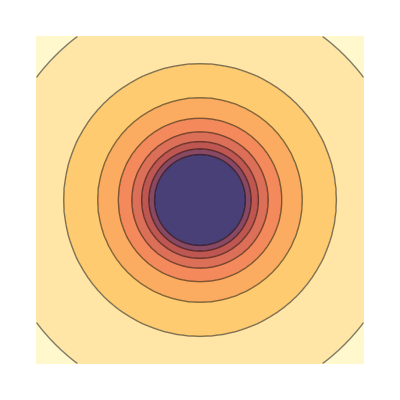
Single Object Gravitational Potential
-Graphics-

```mathematica
Framed[
Column[
{
Style["Single Object Gravitational Potential",Bold,16],
GraphicsRow[
{
Plot3D[gravPotential[1, 1, 1, 0, 0, x, y], {x, -4, 4}, {y, -4, 4},Axes->False],
ContourPlot[gravPotential[1, 1, 1, 0, 0, x, y], {x, -4, 4}, {y, -4, 4}, ClippingStyle->Automatic,Frame->False]
}
]
},
Alignment->Center],
FrameMargins->10]
```

These potentials are additive, so to make the potential for two objects all we need to do is add them together. 
You’ll notice I’ve done a few things to make working with this data easier:

I’ve set m and G to be 1. I only really care about the general shape of the potential, which these won’t impact.

I’ve constrained the system to lie along the X-axis by setting Y to zero.

I’ve constrained the system such that its center of mass is at the origin by setting M1 to position X1 and M2 to position -M1/M2X1.

```mathematica
m:=1
g:=1
twoGrav[M1_, M2_, X1_, X_, Y_]:=gravPotential[M1, m, g, X1, 0, X, Y] + gravPotential[M2, m, g, -M1/M2 X1, 0, X,  Y]
```

In the image below, you can see an equilibrium point between the two masses, where an object will feel an equal pull towards both objects.

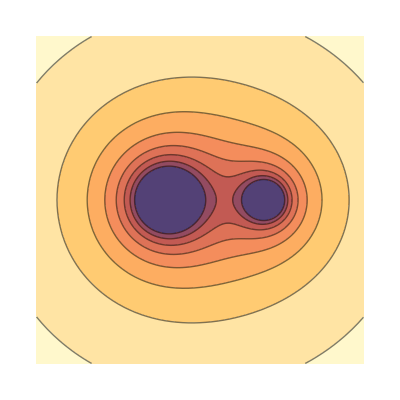
Two Object Gravitational Potential
-Graphics-

```mathematica
Framed[
Column[
{
Style["Two Object Gravitational Potential",Bold,16],
GraphicsRow[
{
Plot3D[twoGrav[2,1, -1, x, y], {x, -5,5}, {y, -5, 5}, PlotPoints->25,Axes->False],
ContourPlot[twoGrav[2,1, -1, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->3,Frame->False]
}
]
},
Alignment->Center],
FrameMargins->10]
```

Next, we tackle the “centrifugal potential”. The physics of this potential is rather nuanced, and but because we are going for intuitive here, I’m not going to spend much time on this point. If you have a ball on a string which you spin in a circle over your head, the ball traces a circular path, and your hand feels a force as though somebody is trying to pull the ball radially away from you. If you change the length of the string while rotating at the same rate, this force changes. 
In our space-based scenario, the two bodies we generate will be circling (i.e. orbiting) around their center of mass. I don’t want generate spinning plots, so we will pretend that the axes of the plots are spinning in lock-step with them. In physics, we’d call this a “rotating reference frame”. The important thing to realize is that objects in orbit experience the same kind of centrifugal potential as in our ball-on-a-rope example above, only instead of a rope they have the force of gravity keeping them bound to the system.

Note: In reality, the rotation rate “w” of the system is dependant on the mass and orbits of our two objects. However, I think it is easier for visualization if we pretend it is some independent thing we can turn on and off.

```mathematica
centrifugal[w_,m_,x_, y_]:= -1/2 w^2*m*EuclideanDistance[{0,0},{x,y}]^2
```

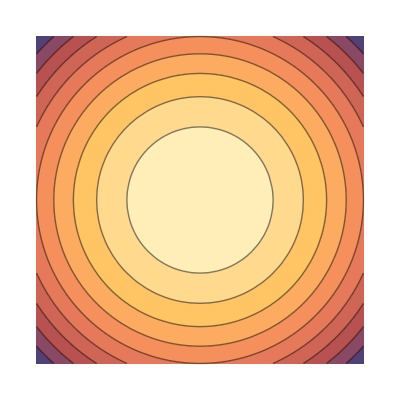
Centrifugal Potential
-Graphics-

```mathematica
Framed[
Column[
{
Style["Centrifugal Potential",Bold,16],
GraphicsRow[
{
Plot3D[centrifugal[1, m, x, y],{x,-5,5},{y,-5,5},Axes->False],
ContourPlot[centrifugal[1, m, x, y],{x,-5,5},{y,-5,5},Frame->False]
}
]
},
Alignment->Center],
FrameMargins->10]
```

## Effective Potential

Just as we could examine the gravitational potential of two masses by adding their individual potentials together, we can do the same with our centrifugal potential.

```mathematica
ratio:=1
separation:=1.5
spin:=0.3
effectivePotential[m_,spin_,ratio_,separation_,x_,y_]:=twoGrav[ratio*m,m, -separation, x, y]+centrifugal[spin,1, x, y]
```

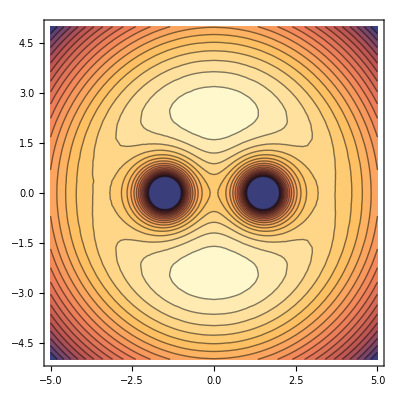
Effective Potential
-Graphics-

```mathematica
Framed[
Column[
{
Style["Effective Potential",Bold,16],
GraphicsRow[
{
Plot3D[effectivePotential[1,0.3,1,1.5,x,y], {x, -5, 5}, {y, -5, 5}, 
ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None],
ContourPlot[effectivePotential[1,0.3,1,1.5,x,y], {x, -5, 5}, {y, -5, 5}, 
ClippingStyle->Automatic, MaxRecursion->2, Contours->20]
}
]
},
Alignment->Center],
FrameMargins->10]
```

## The Lagrange Points

If we imagine this effective potential as a physical surface, the Lagrange points exist at the locations you could place a marble and have it stay perfectly still. To actually plot these points, we need to do a little bit of math. Namely, recall that the force an object feels is equal and opposite to the change in its potential energy (U). Also, recall that force is a vector (it has a magnitude and a direction), where potential energy is a scaler (it has a magnitude, but on direction).

F = -∇U

```mathematica
$Assumptions= x∈Reals && y∈Reals;
force[m_,spin_,ratio_,separation_,x_,y_]:=FunctionExpand[-Grad[effectivePotential[m,spin,ratio,separation,x,y],{x,y}]]
```

The lines in the plot below represent how our hypothetical marble would fall if we placed it at a given point on the surface.

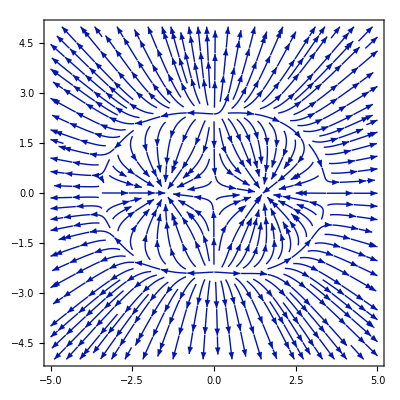

```mathematica
StreamPlot[
Evaluate@force[1,0.3,1,1.5,x,y],
{x,-5,5},{y,-5,5},
StreamPoints->Fine]
```

Mathematically, the Lagrange points exist where the force is zero . We can put this all together to visualize our final system, with the Lagrange points in red..

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

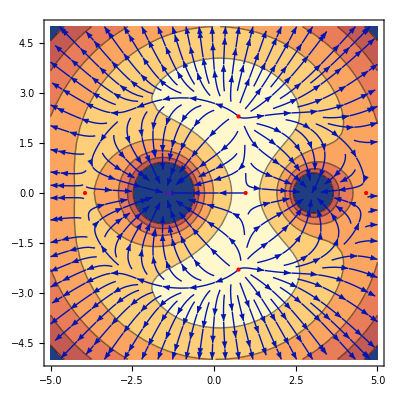
Lagrange Points
-Graphics-

```mathematica
m:=1
spin:=0.3
ratio:=2
separation:=1.5

lagrangePoints:=Solve[force[m,spin,ratio,separation,x,y]==0,{x,y}]

Framed[
Column[
{
Style["Lagrange Points",Bold,16],
GraphicsRow[
{
Plot3D[effectivePotential[m,spin,ratio,separation,x,y], {x, -5, 5}, {y, -5, 5}, 
ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None],
Show[
{
ContourPlot[effectivePotential[m,spin,ratio,separation,x,y], {x, -5, 5}, {y, -5, 5}, 
ClippingStyle->Automatic, MaxRecursion->2, Contours->5],
StreamPlot[
Evaluate@force[m,spin,ratio,separation,x,y],
{x,-5,5},{y,-5,5},
StreamPoints->Automatic],
Graphics[{Red,PointSize[Large],Point[{x,y}/. lagrangePoints]}]
}]
}
]
},
Alignment->Center],
FrameMargins->10]
```

```mathematica
Manipulate[GraphicsColumn[
{
GraphicsRow[
{
Plot3D[twoGrav[ratio*m,m, -separation, x, y],{x, -5, 5}, {y, -5, 5}, 
Mesh->None, 
PlotLabel->"Gravitational Potential",Axes->False],
Plot3D[centrifugal[spin, m, x, y], {x, -5, 5}, {y, -5, 5}, 
Mesh->None, 
PlotLabel->"Centrifugal Potential",Axes->False]
}
],
GraphicsRow[
{
Plot3D[effectivePotential[m,spin,ratio,separation,x,y], {x, -5, 5}, {y, -5, 5}, 
ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, 
PlotLabel->"Effective Potential",Axes->False],
ContourPlot[effectivePotential[m,spin,ratio,separation,x,y], {x, -5, 5}, {y, -5, 5}, 
ClippingStyle->Automatic, MaxRecursion->2, Contours->5, 
PlotLabel->"Effective Potential",Frame->False]
}
]
}
],
{spin,0,1},{separation,0,3},{ratio,1,3}]
```

## Making some Gifs

```mathematica
m:=1
spin:=0.3
ratio:=2
separation:=1.5
Export["spin.gif",Table[
Plot3D[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]],
{spin,0,0.07,0.003}]]
```

spin.gif

```mathematica
mass:=0.01
spin:=0.066
ratio:=1
Export["separation.gif",Table[GraphicsRow[{
Plot3D[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]],
ContourPlot[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30,Contours->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]]}],
{separation,0,1.5, 0.02}]]
```

separation.gif

```mathematica
mass:=0.01
spin:=0.066
separation:=1.5
Export["ratio.gif",Table[GraphicsRow[{
Plot3D[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]],
ContourPlot[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30,Contours->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]]}],
{ratio,1,5,0.1}]]
```

ratio.gif